```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["ErrorBarPlots`"];
```

## Debye mass analytic fitting

### 4-loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=1/16(202/3-20/9 Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3 Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-(8β0[Nf])/(2(4π)^2);
b1[Nf_]=-(32 β1[Nf])/(2(4π)^2);

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+1/(β0[Nf]^7 t^4)( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=SetPrecision[2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1],100];
a4[t_]:=g4[t]^2/(4π);
```

### Parameters

```mathematica
β=SetPrecision[{6.8,6.9,7,7.125,7.25,7.3,7.48},100];
Tvals=SetPrecision[{0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861},100];
Tclatt=SetPrecision[0.1725,100];
Tccont=SetPrecision[{0.155,9},100];
```

```mathematica
md=SetPrecision[{{0.06895350847644509,0.10221807625695377},{0.18664761415678735,0.13994985983632158},{0.2550574027173919,0.15018959554585246},{0.3718613325096623,0.1826759045545378},{0.5260504274058633,0.14840566777365682},{0.542139702256529,0.16900701712235927},{0.6672205262107764,0.1773092554997214}},100];
σmd=SetPrecision[{0.20885132201586987,0.217079251608565,0.22530718120126003,0.23559209319212882,0.2458770051829976,0.2499909699793451,0.26480124324619625},100];
σmderr=SetPrecision[{0.01613174406252025,0.015887095060722983,0.015642446058925716,0.015336634806679135,0.01503082355443255,0.014908499053533919,0.014468130850298837},100];
```

```mathematica
αcont=SetPrecision[{0.5135036591175975,0.0023893085927788557},100]; 
σcont=SetPrecision[{0.16963079795754127,0.00084757894486039},100];
ccont=SetPrecision[{-0.15964102962645102,0.0023730768366581885},100];
```

```mathematica
mDcal[μ_,T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ];
mDcalT[μ_,T_,c_,d_]:=1/T mDcal[μ,T,c,d];
```

### Single fit

#### with 1/T

```mathematica
mDfit=NonlinearModelFit[Table[{Tvals[[n]](155/172.5),md[[n,1]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[Tvals]}],mDcalT[2π,x,d,e],{d,e},x];
{k1,k2}={d,e}/.mDfit["BestFitParameters"];
mDfit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 0.540471 | 0.0599032 | 9.02241 | 0.00027936
e | -0.269885 | 0.0244276 | -11.0484 | 0.000105787

```mathematica
mDfitupper=NonlinearModelFit[Table[{Tvals[[n]](155/172.5),(md[[n,1]]+md[[n,2]])/Tvals[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[Tvals]}],mDcalT[2π,x,d,e],{d,e},x];
{k1u,k2u}={d,e}/.mDfitupper["BestFitParameters"];
mDfitupper["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 0.791313 | 0.063825 | 12.3982 | 0.0000604937
e | -0.327021 | 0.0260268 | -12.5647 | 0.0000566896

```mathematica
mDfitlower=NonlinearModelFit[Table[{Tvals[[n]](155/172.5),(md[[n,1]]-md[[n,2]])/Tvals[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[Tvals]}],mDcalT[2π,x,d,e],{d,e},x];
{k1l,k2l}={d,e}/.mDfitlower["BestFitParameters"];
mDfitlower["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 0.28963 | 0.106124 | 2.72915 | 0.041322
e | -0.212749 | 0.0432759 | -4.91611 | 0.00441234

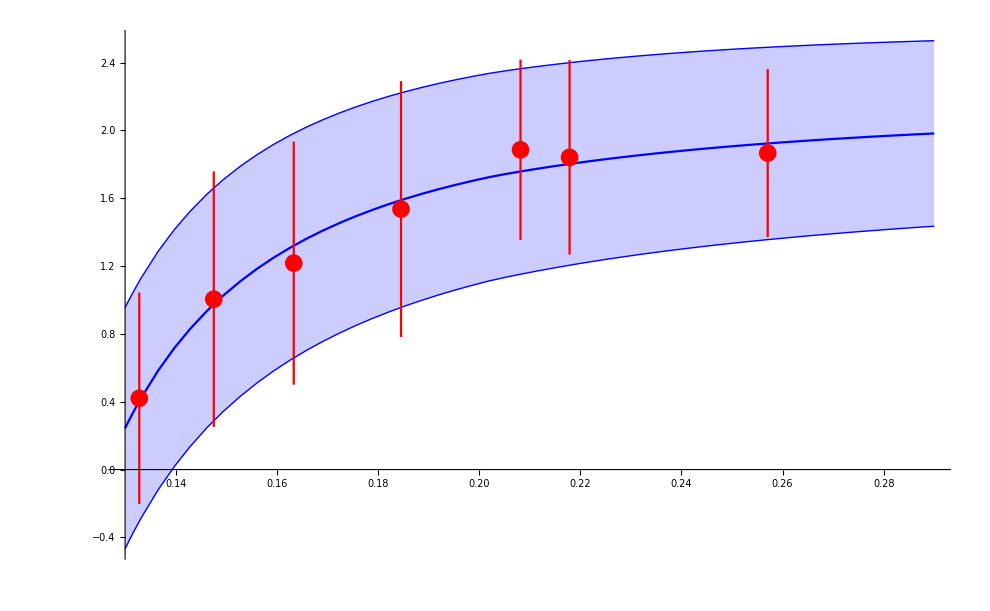

```mathematica
Show[{Plot[{mDcalT[2π,x,k1,k2],mDcalT[2π,x,k1u,k2u],mDcalT[2π,x,k1l,k2l]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{Tvals[[n]](155/172.5),md[[n,1]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]]),md[[n,2]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[β]}],PlotRange->All,PlotStyle->{Red}]}]
```

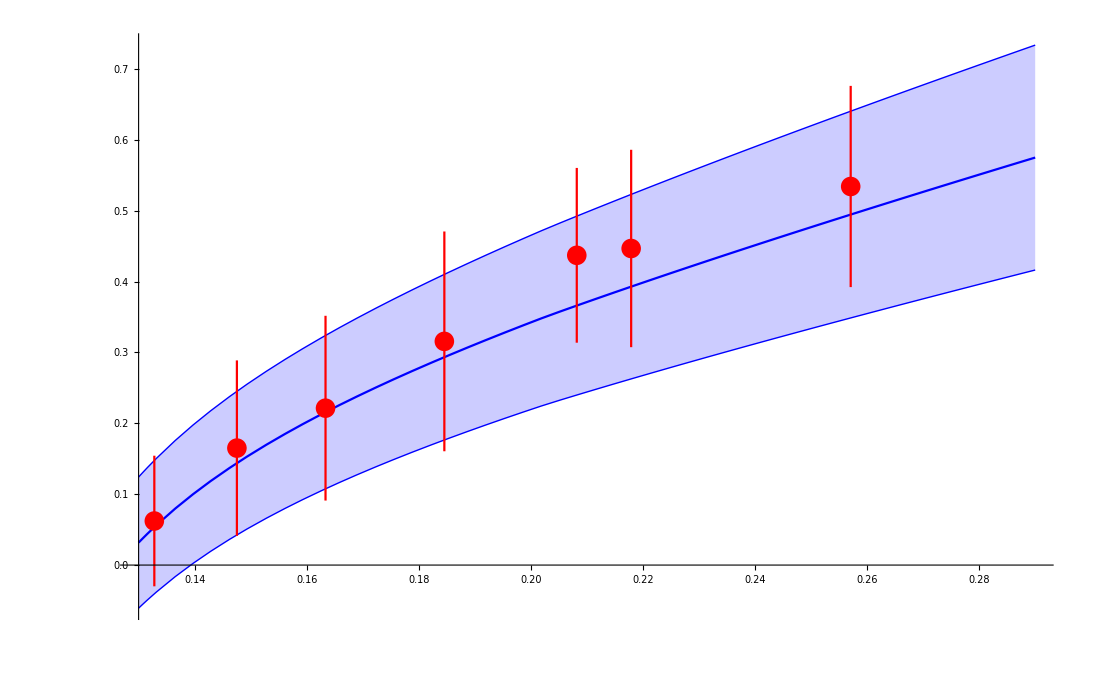

```mathematica
Show[{Plot[{mDcal[2π,x,k1,k2],mDcal[2π,x,k1u,k2u],mDcal[2π,x,k1l,k2l]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{Tvals[[n]](155/172.5),md[[n,1]] √(σcont[[1]]/σmd[[n]]),md[[n,2]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[β]}],PlotRange->All,PlotStyle->{Red}]}]
```

#### without 1/T

```mathematica
mDfit=NonlinearModelFit[Table[{Tvals[[n]](155/172.5),md[[n,1]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[Tvals]}],mDcal[2π,x,d,e],{d,e},x];
{k1,k2}={d,e}/.mDfit["BestFitParameters"];
mDfit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 0.728087 | 0.0727653 | 10.006 | 0.000170459
e | -0.336358 | 0.0309103 | -10.8818 | 0.000113839

```mathematica
mDfitupper=NonlinearModelFit[Table[{Tvals[[n]](155/172.5),(md[[n,1]]+md[[n,2]])^1 √(σcont[[1]]/σmd[[n]])},{n,1,Length[Tvals]}],mDcal[2π,x,d,e],{d,e},x];
{k1u,k2u}={d,e}/.mDfitupper["BestFitParameters"];
mDfitupper["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 0.960701 | 0.0762147 | 12.6052 | 0.0000558096
e | -0.380869 | 0.0323756 | -11.7641 | 0.0000780662

```mathematica
mDfitlower=NonlinearModelFit[Table[{Tvals[[n]](155/172.5),(md[[n,1]]-md[[n,2]])^1 √(σcont[[1]]/σmd[[n]])},{n,1,Length[Tvals]}],mDcal[2π,x,d,e],{d,e},x];
{k1l,k2l}={d,e}/.mDfitlower["BestFitParameters"];
mDfitlower["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 0.495473 | 0.120467 | 4.11293 | 0.00923743
e | -0.291847 | 0.0511738 | -5.70306 | 0.00231409

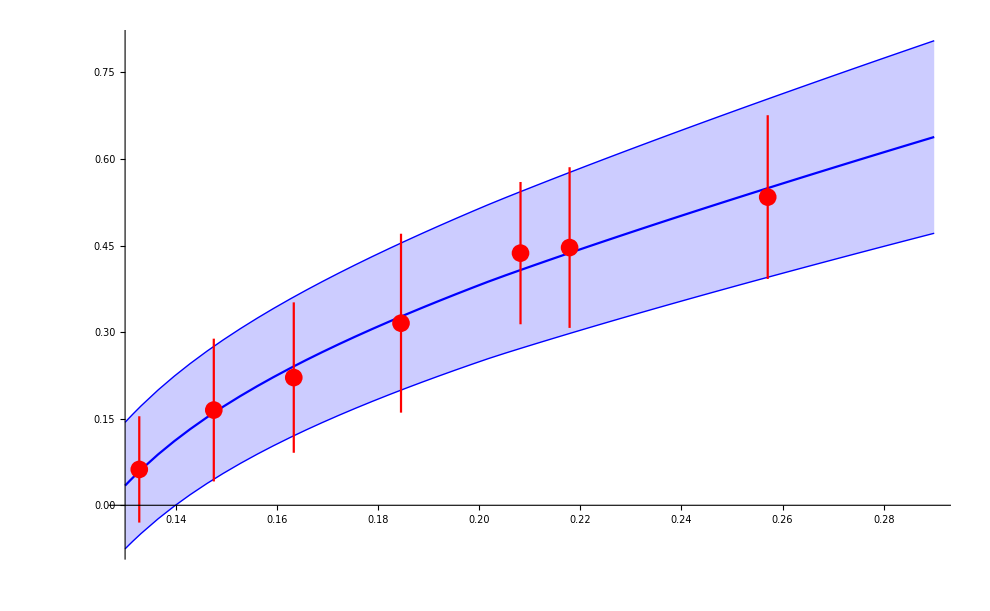

```mathematica
Show[{Plot[{mDcal[2π,x,k1,k2],mDcal[2π,x,k1u,k2u],mDcal[2π,x,k1l,k2l]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{Tvals[[n]](155/172.5),md[[n,1]] √(σcont[[1]]/σmd[[n]]),md[[n,2]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[β]}],PlotRange->All,PlotStyle->{Red}]}]
```

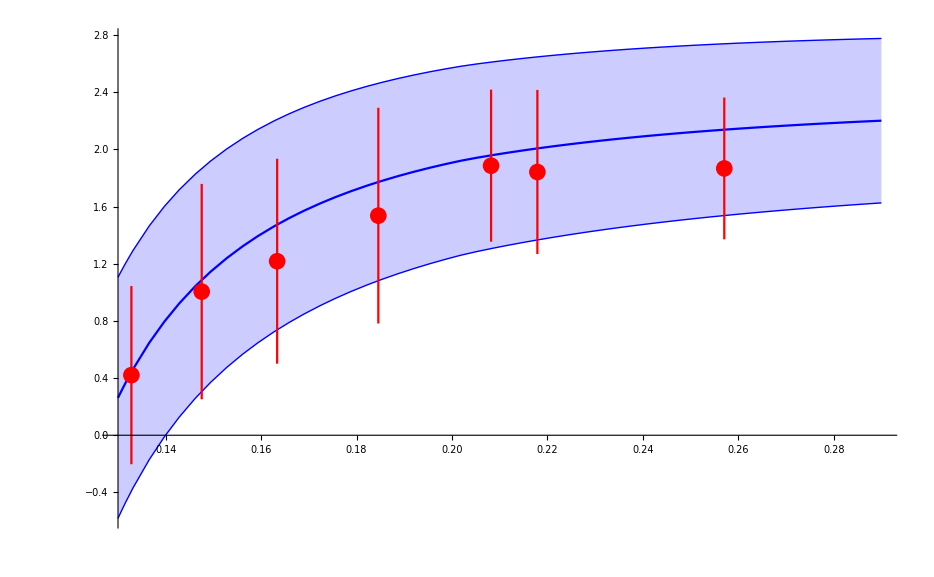

```mathematica
Show[{Plot[{mDcalT[2π,x,k1,k2],mDcalT[2π,x,k1u,k2u],mDcalT[2π,x,k1l,k2l]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{Tvals[[n]](155/172.5),md[[n,1]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]]),md[[n,2]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[β]}],PlotRange->All,PlotStyle->{Red}]}]
```

### Multiple fitting

```mathematica
ParallelSow[exp_,tag_]:=Sow[exp,tag];
SetSharedFunction[ParallelSow];
```

```mathematica
mdrandu[n_]:=Block[{m},m=md[[n,1]]+Abs[RandomVariate[NormalDistribution[0,md[[n,2]]]]];If[m>0,m,0]]
mdrandl[n_]:=Block[{m},m=md[[n,1]]-Abs[RandomVariate[NormalDistribution[0,md[[n,2]]]]];If[m>0,m,0]]
σrand[n_]:=RandomVariate[NormalDistribution[σmd[[n]],σmderr[[n]]]];
σcontrand:=RandomVariate[NormalDistribution[σcont[[1]],σcont[[2]]]];
```

#### with 1/T

```mathematica
temp=Reap[Block[{k1u,k2u,k1l,k2l},ParallelDo[Quiet[{k1u,k2u}={d,e}/.NonlinearModelFit[Table[{Tvals[[n]](155/172.5),mdrandu[n]/Tvals[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[Tvals]}],mDcalT[2π,x,d,e],{d,e},x]["BestFitParameters"];
{k1l,k2l}={d,e}/.NonlinearModelFit[Table[{Tvals[[n]](155/172.5),mdrandl[n]/Tvals[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[Tvals]}],mDcalT[2π,x,d,e],{d,e},x]["BestFitParameters"]];
ParallelSow[k1u,d1u];
ParallelSow[k2u,e1u];
ParallelSow[k1l,d2l];
ParallelSow[k2l,e2l];,{i,1,10}]],{d1u,e1u,d2l,e2l}];//AbsoluteTiming
kfinalu={Mean[temp[[2,1,1]]],Mean[temp[[2,2,1]]]}
kfinall={Mean[temp[[2,3,1]]],Mean[temp[[2,4,1]]]}
kfinal={Mean[{kfinalu[[1]],kfinall[[1]]}],Mean[{kfinalu[[2]],kfinall[[2]]}]}
kerror={kfinalu[[1]]-kfinal[[1]],kfinal[[2]]-kfinalu[[2]]};
Clear[temp];
```

{0.630845,Null}

{0.730395,-0.313544}

{0.341244,-0.219802}

{0.53582,-0.266673}

```mathematica
(*kfinal={0.4709613222916442,-0.2550225519531524};(*100k run*)
kfinalu={0.8020780608066254,-0.360468820434673};
kfinall={0.13984458377666326,-0.14957628347163182};*)
```

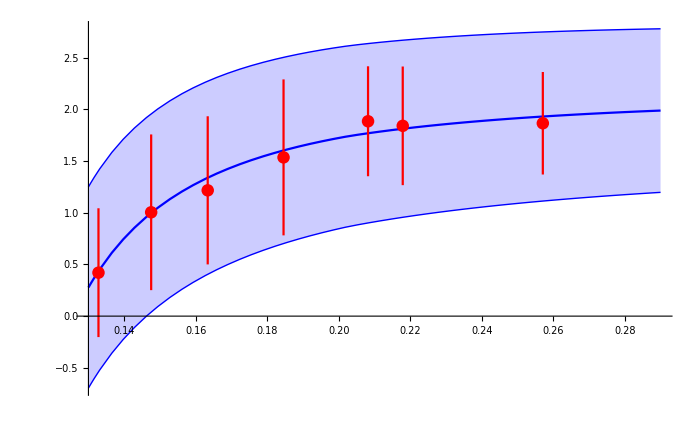

```mathematica
Show[{Plot[{mDcalT[2π,x,kfinal[[1]],kfinal[[2]]],mDcalT[2π,x,kfinal[[1]]+1.96 kerror[[1]],kfinal[[2]]-1.96 kerror[[2]]],mDcalT[2π,x,kfinal[[1]]-1.96 kerror[[1]],kfinal[[2]]+1.96 kerror[[2]]]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{Tvals[[n]](155/172.5),md[[n,1]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]]),md[[n,2]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[β]}],PlotRange->All,PlotStyle->{Red}]}]
```

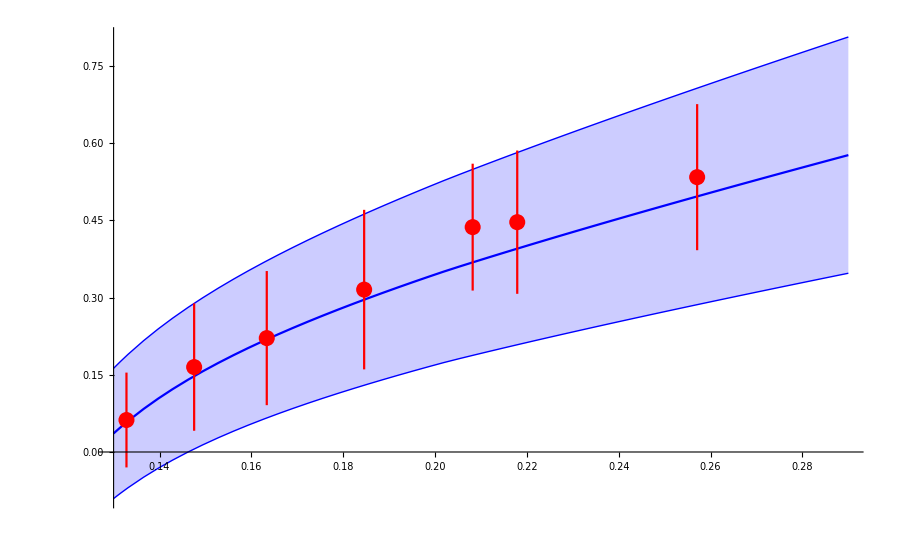

```mathematica
Show[{Plot[{mDcal[2π,x,kfinal[[1]],kfinal[[2]]],mDcal[2π,x,kfinal[[1]]+1.96 kerror[[1]],kfinal[[2]]-1.96 kerror[[2]]],mDcal[2π,x,kfinal[[1]]-1.96 kerror[[1]],kfinal[[2]]+1.96 kerror[[2]]]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{Tvals[[n]](155/172.5),md[[n,1]] √(σcont[[1]]/σmd[[n]]),md[[n,2]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[β]}],PlotRange->All,PlotStyle->{Red}]}]
```

#### without 1/T

```mathematica
temp=Reap[Block[{k1u,k2u,k1l,k2l},ParallelDo[Quiet[{k1u,k2u}={d,e}/.NonlinearModelFit[Table[{Tvals[[n]](155/172.5),mdrandu[n] √(σcont[[1]]/σmd[[n]])},{n,1,Length[Tvals]}],mDcal[2π,x,d,e],{d,e},x]["BestFitParameters"];
{k1l,k2l}={d,e}/.NonlinearModelFit[Table[{Tvals[[n]](155/172.5),mdrandl[n] √(σcont[[1]]/σmd[[n]])},{n,1,Length[Tvals]}],mDcal[2π,x,d,e],{d,e},x]["BestFitParameters"]];
ParallelSow[k1u,d1u];
ParallelSow[k2u,e1u];
ParallelSow[k1l,d2l];
ParallelSow[k2l,e2l];,{i,1,10000}]],{d1u,e1u,d2l,e2l}];//AbsoluteTiming
kfinalu={Mean[temp[[2,1,1]]],Mean[temp[[2,2,1]]]}
kfinall={Mean[temp[[2,3,1]]],Mean[temp[[2,4,1]]]}
kfinal={Mean[{kfinalu[[1]],kfinall[[1]]}],Mean[{kfinalu[[2]],kfinall[[2]]}]}
kerror={kfinalu[[1]]-kfinal[[1]],kfinal[[2]]-kfinalu[[2]]};
Clear[temp];
```

{337.426,Null}

{0.916912,-0.373171}

{0.46437,-0.26455}

{0.690641,-0.318861}

```mathematica
(*kfinal={0.4709613222916442,-0.2550225519531524};(*100k run*)
kfinalu={0.8020780608066254,-0.360468820434673};
kfinall={0.13984458377666326,-0.14957628347163182};*)
```

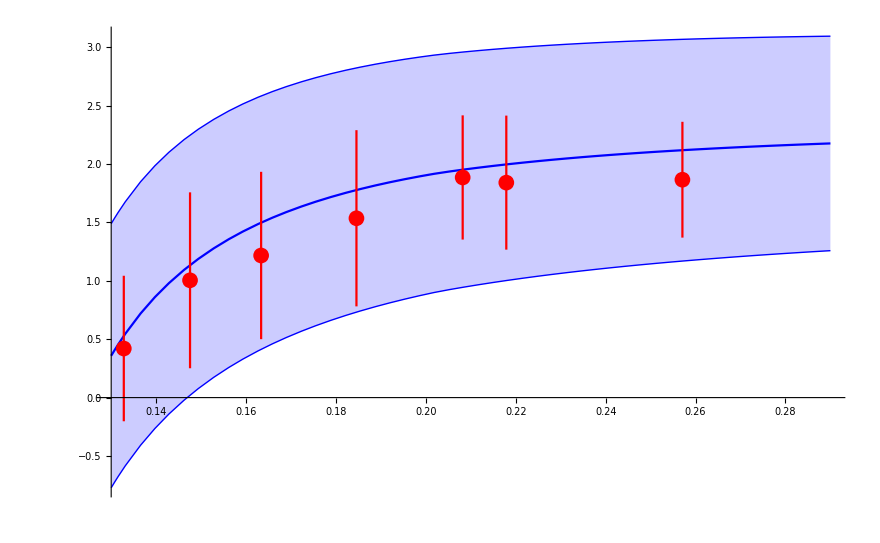

```mathematica
Show[{Plot[{mDcalT[2π,x,kfinal[[1]],kfinal[[2]]],mDcalT[2π,x,kfinal[[1]]+1.96 kerror[[1]],kfinal[[2]]-1.96 kerror[[2]]],mDcalT[2π,x,kfinal[[1]]-1.96 kerror[[1]],kfinal[[2]]+1.96 kerror[[2]]]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{Tvals[[n]](155/172.5),md[[n,1]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]]),md[[n,2]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[β]}],PlotRange->All,PlotStyle->{Red}]}]
```

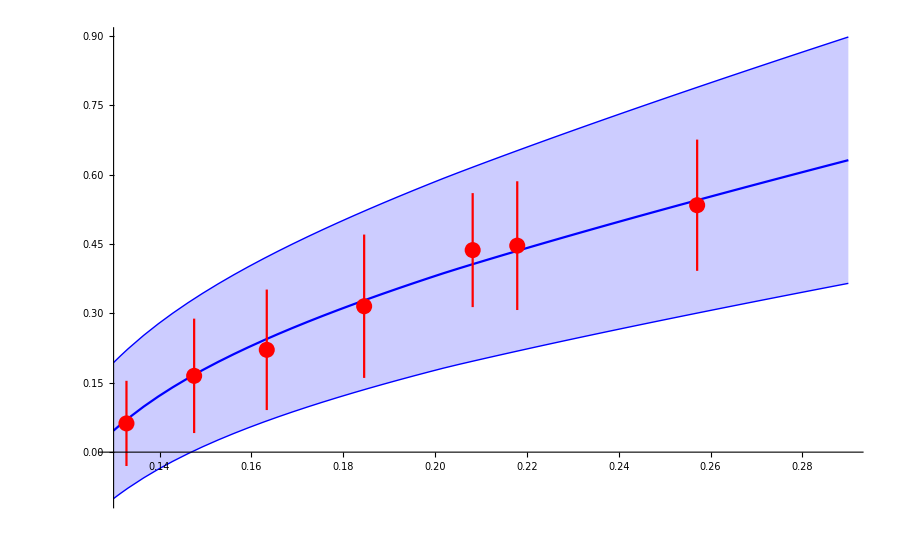

```mathematica
Show[{Plot[{mDcal[2π,x,kfinal[[1]],kfinal[[2]]],mDcal[2π,x,kfinal[[1]]+1.96 kerror[[1]],kfinal[[2]]-1.96 kerror[[2]]],mDcal[2π,x,kfinal[[1]]-1.96 kerror[[1]],kfinal[[2]]+1.96 kerror[[2]]]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{Tvals[[n]](155/172.5),md[[n,1]] √(σcont[[1]]/σmd[[n]]),md[[n,2]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[β]}],PlotRange->All,PlotStyle->{Red}]}]
```

### Braten - Nieto expression

```mathematica
ngam[x_]:=PolyGamma[1/2-ⅈ x]+PolyGamma[1/2+ⅈ x];
mDBNT[T_,μ_,c_,d_]:=(4π)/3 a4[2π √(T^2+μ^2/π^2)](Nc+(Nc^2 a4[2π √(T^2+μ^2/π^2)])/(12π)(5+22 EulerGamma+22Log[(2π √(T^2+μ^2/π^2))/(4π T)])+nf[2π √(T^2+μ^2/π^2)]/2(1+12 μ^2/(2π T)^2)+(Nc nf[2π √(T^2+μ^2/π^2)] a4[2π √(T^2+μ^2/π^2)])/(24π)((9+132 μ^2/(2π T)^2)+22EulerGamma(1+12 μ^2/(2π T)^2)+2(7+132 μ^2/(2π T)^2)Log[(2π √(T^2+μ^2/π^2))/(4π T)]+4ngam[μ/(2π T)])+(nf[2π √(T^2+μ^2/π^2)]^2 a4[2π √(T^2+μ^2/π^2)])/(12π)(1+12 μ^2/(2π T)^2)(1-2Log[(2π √(T^2+μ^2/π^2))/(4π T)]+ngam[μ/(2π T)])-3/(8π)(nf[2π √(T^2+μ^2/π^2)](Nc^2-1)a4[2π √(T^2+μ^2/π^2)])/Nc(1+12 μ^2/(2π T)^2)+c a4[2π √(T^2+μ^2/π^2)]^2+d a4[2π √(T^2+μ^2/π^2)]^3);
```

```mathematica
mDBNfit=NonlinearModelFit[Table[{Tvals[[n]](155/172.5),(md[[n,1]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]]))^2},{n,1,Length[Tvals]}],mDBNT[x,0,d,e],{d,e},x];
{k1,k2}={d,e}/.mDBNfit["BestFitParameters"];
mDBNfit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | -28.5565 | 2.80267 | -10.189 | 0.000156254
e | 29.672 | 5.16832 | 5.74113 | 0.00224689

```mathematica
mDBNfitu=NonlinearModelFit[Table[{Tvals[[n]](155/172.5),((md[[n,1]]+md[[n,2]])/Tvals[[n]] √(σcont[[1]]/σmd[[n]]))^2},{n,1,Length[Tvals]}],mDBNT[x,0,d,e],{d,e},x];
{k1u,k2u}={d,e}/.mDBNfitu["BestFitParameters"];
mDBNfitu["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | -5.1405 | 5.45775 | -0.941871 | 0.389504
e | -9.46476 | 10.0645 | -0.940411 | 0.390183

```mathematica
mDBNfitl=NonlinearModelFit[Table[{Tvals[[n]](155/172.5),((md[[n,1]]-md[[n,2]])/Tvals[[n]] √(σcont[[1]]/σmd[[n]]))^2},{n,1,Length[Tvals]}],mDBNT[x,0,d,e],{d,e},x];
{k1l,k2l}={d,e}/.mDBNfitl["BestFitParameters"];
mDBNfitl["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | -44.1191 | 1.5032 | -29.3501 | 8.60729×10^-7
e | 56.2725 | 2.77201 | 20.3003 | 5.36499×10^-6

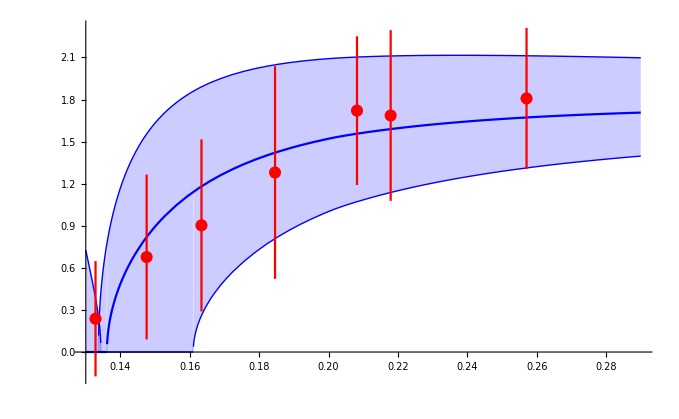

```mathematica
Show[{Plot[{Re[Sqrt[mDBNT[x,0.,k1,k2]]],Re[Sqrt[mDBNT[x,0.,k1u,k2u]]],Re[Sqrt[mDBNT[x,0.,k1l,k2l]]]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{Tvals[[n]](155/172.5),md[[n,1]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]]),md[[n,2]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[Tvals]}],PlotRange->All,PlotStyle->{Red}]}]
```

```mathematica
BNfitsu={{},{}};
BNfitsl={{},{}};
SetSharedVariable[BNfitsu,BNfitsl];
Module[{k1u,k2u,k1l,k2l},ParallelDo[Quiet[{k1u,k2u}={d,e}/.NonlinearModelFit[Table[{Tvals[[n]](155/172.5),(mdrandu[n]/Tvals[[n]] √(σcont[[1]]/σmd[[n]]))^2},{n,1,Length[Tvals]}],mDBNT[x,0,d,e],{d,e},x]["BestFitParameters"];
{k1l,k2l}={d,e}/.NonlinearModelFit[Table[{Tvals[[n]](155/172.5),(mdrandl[n]/Tvals[[n]] √(σcont[[1]]/σmd[[n]]))^2},{n,1,Length[Tvals]}],mDBNT[x,0,d,e],{d,e},x]["BestFitParameters"]];
BNfitsu[[1]]=Append[BNfitsu[[1]],k1u];
BNfitsu[[2]]=Append[BNfitsu[[2]],k2u];
BNfitsl[[1]]=Append[BNfitsl[[1]],k1l];BNfitsl[[2]]=Append[BNfitsl[[2]],k2l],{i,1,100000}]]//AbsoluteTiming
```

{10518.6,Null}

```mathematica
BNkfinalu={Mean[BNfitsu[[1]]],Mean[BNfitsu[[2]]]}
BNkfinall={Mean[BNfitsl[[1]]],Mean[BNfitsl[[2]]]}
```

{-9.10463,-2.78162}

{-40.116,49.4044}

```mathematica
BNkfinal={Mean[{BNkfinalu[[1]],BNkfinall[[1]]}],Mean[{BNkfinalu[[2]],BNkfinall[[2]]}]}(*100k run*)
```

{-24.6103,23.3114}

```mathematica
Export["BNkfinalRESu.dat",BNkfinalu]
Export["BNkfinalRESl.dat",BNkfinall]
Export["BNkfinalRES.dat",BNkfinal]
```

BNkfinalRESu.dat

BNkfinalRESl.dat

BNkfinalRES.dat

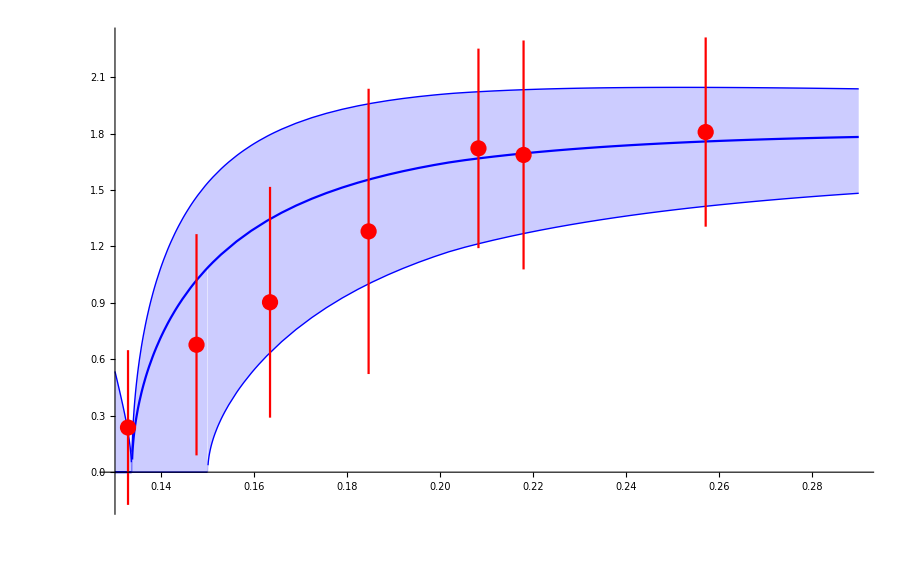

```mathematica
Show[{Plot[{Re[Sqrt[mDBNT[x,0.,BNkfinal[[1]],BNkfinal[[2]]]]],Re[Sqrt[mDBNT[x,0.,BNkfinalu[[1]],BNkfinalu[[2]]]]],Re[Sqrt[mDBNT[x,0.,BNkfinall[[1]],BNkfinall[[2]]]]]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{Tvals[[n]](155/172.5),md[[n,1]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]]),md[[n,2]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[Tvals]}],PlotRange->All,PlotStyle->{Red}]}]
```